```mathematica
Bϕ[R_]:=B0 R/L Exp[1-R/L]
Jz[R_]:=1/R D[r Bϕ[r],r]/.r->R
FR[R_]:=Jz[R]Bϕ[R]
P[R_]:=P0+Integrate[FR[r],{r,0,R}]
```

```mathematica
Jz[R]Bϕ[R]-P'[R]//Simplify
```

0

```mathematica
P[R]//FullSimplify
```

P0+(B0^2 ⅇ^2 (L^2-ⅇ^(-(2 R)/L) (L^2+2 L R-2 R^2)))/(4 L^2)

## P0+(B0^2 ⅇ^2)/4 (1-ⅇ^(-(2 R)/L) (1+2 R/L(1-R/L)))

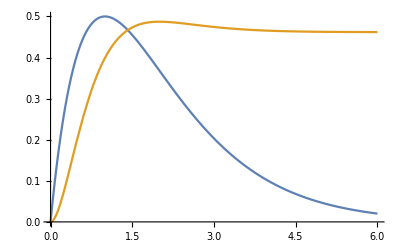

```mathematica
params={L->1,B0->0.5,P0->0};
p=P[R]/.params;
b=Bϕ[R]/.params;
Plot[{b,p},{R,0,6}]
```